```mathematica
BlockchainBlockData[]
```

BlockchainBlockData::argn: BlockchainBlockData called with 0 arguments; 1 or 2 arguments are expected.

$Failed

```mathematica
FinancialData["NASDAQ:GOOG","Price"]
```

Missing[NotAvailable]

```mathematica
amzn=FinancialData["NASDAQ:AMZN","Price",All]
```

TimeSeries[…]

```mathematica
amzndiff=Reverse@
Transpose[{
amzn["Dates"][[;;-2]],
Differences@amzn["Values"]
}];
```

```mathematica
Histogram[Map[Last,amzndiff],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Histogram[Map[Last,amzndiff],
PlotRange->{{-100,100},{0,2000}},PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
MemoryInUse[]
```

298184336

```mathematica
Quartiles[Map[Last,amzndiff]]
```

{-1.23 $,0.03 $,1.51 $}

```mathematica
Table[i/10,{i,1,10,1}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Quantile[Map[Last,amzndiff],{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
```

{-4.44 $,-1.84 $,-0.79 $,-0.27 $,0.03 $,0.39 $,1.00 $,2.42 $,5.82 $,128.52 $}

```mathematica
Grid@
Map[{#,Quantile[Map[Last,amzndiff],#]}&,{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
```

1/10 | -4.44 $
1/5 | -1.84 $
3/10 | -0.79 $
2/5 | -0.27 $
1/2 | 0.03 $
3/5 | 0.39 $
7/10 | 1.00 $
4/5 | 2.42 $
9/10 | 5.82 $
1 | 128.52 $

```mathematica
Grid@
Map[{PercentForm@N@#,Quantile[Map[Last,amzndiff],#]}&,{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
```

10% | -4.44 $
20% | -1.84 $
30% | -0.79 $
40% | -0.27 $
50% | 0.03 $
60% | 0.39 $
70% | 1.00 $
80% | 2.42 $
90% | 5.82 $
100% | 128.52 $

```mathematica
Grid@
Map[{PercentForm@N@#,Quantile[Map[Last,amzndiff],#]}&,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
```

0% | -139.36 $
10% | -4.44 $
20% | -1.84 $
30% | -0.79 $
40% | -0.27 $
50% | 0.03 $
60% | 0.39 $
70% | 1.00 $
80% | 2.42 $
90% | 5.82 $
100% | 128.52 $

```mathematica
DateListPlot[amzn,
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

```mathematica
Histogram[Map[Last,amzndiff],
PlotRange->{{-100,100},{0,2000}},PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Histogram[Map[Last,amzndiff],{1},
PlotRange->{{-100,100},{0,2000}},PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Histogram[Map[Last,amzndiff],{1},
PlotRange->{{-100,100},Full},PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
DateListPlot[amzn,
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
TradingChart[{}]
```

TradingChart::ldata: {} is not a valid dataset or list of datasets.

TradingChart[{}]

```mathematica
TradingChart[]
```

TradingChart::argt: TradingChart called with 0 arguments; 1 or 2 arguments are expected.

TradingChart[]

```mathematica
Grid@
TakeLargestBy[amzndiff,Last,10]
```

Thu 26 Oct 2017 00:00:00GMT-7. | 128.52 $
Mon 24 Dec 2018 00:00:00GMT-7. | 126.94 $
Wed 24 Oct 2018 00:00:00GMT-7. | 117.97 $
Tue 6 Nov 2018 00:00:00GMT-7. | 112.68 $
Tue 27 Nov 2018 00:00:00GMT-7. | 96.33 $
Fri 30 Nov 2018 00:00:00GMT-7. | 82.19 $
Fri 23 Nov 2018 00:00:00GMT-7. | 79.27 $
Tue 29 Jan 2019 00:00:00GMT-7. | 76.55 $
Thu 3 Jan 2019 00:00:00GMT-7. | 75.11 $
Thu 11 Oct 2018 00:00:00GMT-7. | 69.25 $

```mathematica
Grid@
Map[
{PercentForm@N@#,Quantile[Map[Last,amzndiff],#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
```

0% | -139.36 $
10% | -4.44 $
20% | -1.84 $
30% | -0.79 $
40% | -0.27 $
50% | 0.03 $
60% | 0.39 $
70% | 1.00 $
80% | 2.42 $
90% | 5.82 $
100% | 128.52 $

```mathematica
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
]
]
```

Grid[Map[{N[Slot[100%]],Quantile[{15.23 $,11.19 $,22.42 $,0.26 $,10.46 $,14.39 $,28.49 $,26.72 $,43.69 $,8.86 $,27.34 $,4.04 $,5.09 $,14.71 $,31.50 $,4.21 $,20.56 $,2.44 $,10.80 $,2.16 $,7.21 $,40.10 $,10.78 $,13.55 $,10.11 $,22.15 $,2.42 $,7.04 $,19.25 $,55.98 $,17.94 $,22.16 $,14.74 $,23.55 $,16.45 $,13.16 $,61.38 $,39.42 $,22.66 $,25.31 $,39.49 $,5.57 $,22.70 $,58.11 $,32.08 $,11.46 $,31.75 $,13.92 $,30.60 $,30.77 $,26.99 $,6.32 $,8.86 $,21.11 $,13.38 $,14.13 $,17.87 $,11.09 $,9.99 $,9.93 $,16.34 $,29.11 $,35.98 $,9.41 $,3.91 $,4.69 $,12.12 $,28.56 $,10.65 $,6.45 $,19.56 $,35.63 $,2.60 $,6.89 $,9.40 $,7.42 $,15.34 $,16.36 $,0.63 $,14.98 $,8.38 $,3.07 $,56.60 $,49.67 $,15.86 $,8.94 $,36.87 $,82.38 $,41.25 $,2.87 $,17.24 $,13.15 $,7.80 $,44.20 $,2.16 $,1.45 $,10.03 $,38.57 $,36.42 $,31.03 $,17.44 $,67.30 $,9.89 $,17.90 $,3.23 $,29.55 $,11.91 $,61.64 $,10.70 $,15.00 $,11.91 $,12.20 $,48.38 $,0.50 $,22.02 $,36.46 $,25.62 $,3.13 $,1.78 $,18.17 $,1.81 $,1.01 $,3.26 $,11.49 $,14.02 $,12.58 $,18.42 $,1.84 $,6.72 $,5378,0.31 $,0.09 $,0.18 $,0.26 $,0.27 $,0.18 $,0.21 $,0.08 $,0.11 $,0.01 $,0.04 $,0.27 $,0.44 $,0.68 $,0.76 $,0.53 $,0.02 $,0.09 $,0.60 $,0.20 $,0.00 $,0.30 $,0.06 $,0.02 $,0.10 $,0.15 $,0.26 $,0.05 $,0.07 $,0.11 $,0.00 $,0.01 $,0.32 $,0.30 $,0.13 $,0.09 $,0.30 $,0.25 $,0.13 $,0.55 $,0.66 $,0.12 $,0.05 $,0.26 $,0.59 $,0.53 $,0.15 $,0.06 $,0.24 $,0.50 $,0.05 $,0.22 $,0.02 $,0.02 $,0.04 $,0.06 $,0.03 $,0.13 $,0.09 $,0.01 $,0.05 $,0.00 $,0.13 $,0.07 $,0.04 $,0.04 $,0.00 $,0.13 $,0.04 $,0.12 $,0.07 $,0.04 $,0.10 $,0.10 $,0.02 $,0.05 $,0.03 $,0.16 $,0.09 $,0.03 $,0.03 $,0.16 $,0.05 $,0.03 $,0.06 $,0.12 $,0.20 $,0.00 $,0.16 $,0.27 $,0.24 $,0.02 $,0.30 $,0.09 $,0.32 $,0.07 $,0.03 $,0.05 $,0.02 $,0.00 $,0.00 $,0.01 $,0.03 $,0.01 $,0.02 $,0.00 $,0.07 $,0.01 $,0.02 $,0.06 $,0.04 $,0.10 $,0.03 $,0.11 $,0.13 $,0.06 $,0.03 $,0.01 $,0.01 $,0.03 $,0.05 $,0.08 $,0.10 $,0.03 $,0.21 $,0.07 $,0.02 $,0.23 $},2]}&]]
 |  |  |  |

```mathematica
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
]
```

0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $

```mathematica
With[{abs=Map[Abs@Last@#&,amzndiff]},
Histogram[abs,{1},
PlotRange->{{0,100},Full},PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
```

-Graphics-

```mathematica
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
]
```

0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $

```mathematica
Grid@
amzndiff[[;;10]]
```

Thu 3 Oct 2019 00:00:00GMT-7. | 15.23 $
Wed 2 Oct 2019 00:00:00GMT-7. | 11.19 $
Tue 1 Oct 2019 00:00:00GMT-7. | -22.42 $
Mon 30 Sep 2019 00:00:00GMT-7. | -0.26 $
Fri 27 Sep 2019 00:00:00GMT-7. | 10.46 $
Thu 26 Sep 2019 00:00:00GMT-7. | -14.39 $
Wed 25 Sep 2019 00:00:00GMT-7. | -28.49 $
Tue 24 Sep 2019 00:00:00GMT-7. | 26.72 $
Mon 23 Sep 2019 00:00:00GMT-7. | -43.69 $
Fri 20 Sep 2019 00:00:00GMT-7. | -8.86 $

```mathematica
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Map[Function[val,{val,PercentForm@((Length@Select[diff,val>#&])/len)}],values]
]]
```

{{15.23 $,5437/5635},{11.19 $,5352/5635},{-22.42 $,3/161},{-0.26 $,2267/5635},{10.46 $,761/805},{-14.39 $,157/5635},{-28.49 $,16/1127},{26.72 $,5552/5635},{-43.69 $,38/5635},{-8.86 $,54/1127}}

```mathematica
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
```

15.23 $ | 96.49%
11.19 $ | 94.98%
-22.42 $ | 1.863%
-0.26 $ | 40.23%
10.46 $ | 94.53%
-14.39 $ | 2.786%
-28.49 $ | 1.42%
26.72 $ | 98.53%
-43.69 $ | 0.6744%
-8.86 $ | 4.791%

```mathematica
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
]
```

0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $

```mathematica
DateListPlot[Reverse@amzndiff,
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
DateListPlot[Reverse@Map[Tooltip,amzndiff],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
DateString[DateObject[{2019,10,1,0,0,0.},"Instant","Gregorian",-7.]]
```

Tue 1 Oct 2019 00:00:00

```mathematica
DateListPlot[Reverse@Map[Tooltip[#,{DateString@First@#,Last@#}]&,amzndiff],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
FinancialData["
```

```mathematica
{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}
```

{0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $,15.23 $ | 96.49%
11.19 $ | 94.98%
-22.42 $ | 1.863%
-0.26 $ | 40.23%
10.46 $ | 94.53%
-14.39 $ | 2.786%
-28.49 $ | 1.42%
26.72 $ | 98.53%
-43.69 $ | 0.6744%
-8.86 $ | 4.791%}

```mathematica
FinancialData["NASDAQ:AMZN","Price",{2018}]
```

TimeSeries[…]

```mathematica
amzndiff2018=Reverse@
Transpose[{
Out[39]["Dates"][[;;-2]],
Differences@
Out[39]["Values"]
}]
```

{{Thu 3 Oct 2019 00:00:00GMT-7.,15.23 $},{Wed 2 Oct 2019 00:00:00GMT-7.,11.19 $},{Tue 1 Oct 2019 00:00:00GMT-7.,-22.42 $},{Mon 30 Sep 2019 00:00:00GMT-7.,-0.26 $},{Fri 27 Sep 2019 00:00:00GMT-7.,10.46 $},{Thu 26 Sep 2019 00:00:00GMT-7.,-14.39 $},{Wed 25 Sep 2019 00:00:00GMT-7.,-28.49 $},{Tue 24 Sep 2019 00:00:00GMT-7.,26.72 $},426,{Wed 10 Jan 2018 00:00:00GMT-7.,22.35 $},{Tue 9 Jan 2018 00:00:00GMT-7.,1.63 $},{Mon 8 Jan 2018 00:00:00GMT-7.,5.83 $},{Fri 5 Jan 2018 00:00:00GMT-7.,17.73 $},{Thu 4 Jan 2018 00:00:00GMT-7.,19.55 $},{Wed 3 Jan 2018 00:00:00GMT-7.,5.39 $},{Tue 2 Jan 2018 00:00:00GMT-7.,15.19 $}}
 |  |  |  |

```mathematica
With[{amzndiff=amzndiff2018},{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}
]
```

{0% | 0.00 $
10% | 2.66 $
20% | 6.11 $
30% | 9.63 $
40% | 12.58 $
50% | 16.60 $
60% | 21.44 $
70% | 27.66 $
80% | 36.87 $
90% | 56.40 $
100% | 139.36 $,15.23 $ | 69.16%
11.19 $ | 63.49%
-22.42 $ | 18.14%
-0.26 $ | 42.63%
10.46 $ | 61.68%
-14.39 $ | 24.04%
-28.49 $ | 14.74%
26.72 $ | 83.9%
-43.69 $ | 8.163%
-8.86 $ | 31.07%}

```mathematica
{
With[{amzndiff=amzndiff2018},{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}
]
,
{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}}
```

{{0% | 0.00 $
10% | 2.66 $
20% | 6.11 $
30% | 9.63 $
40% | 12.58 $
50% | 16.60 $
60% | 21.44 $
70% | 27.66 $
80% | 36.87 $
90% | 56.40 $
100% | 139.36 $,15.23 $ | 69.16%
11.19 $ | 63.49%
-22.42 $ | 18.14%
-0.26 $ | 42.63%
10.46 $ | 61.68%
-14.39 $ | 24.04%
-28.49 $ | 14.74%
26.72 $ | 83.9%
-43.69 $ | 8.163%
-8.86 $ | 31.07%},{0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $,15.23 $ | 96.49%
11.19 $ | 94.98%
-22.42 $ | 1.863%
-0.26 $ | 40.23%
10.46 $ | 94.53%
-14.39 $ | 2.786%
-28.49 $ | 1.42%
26.72 $ | 98.53%
-43.69 $ | 0.6744%
-8.86 $ | 4.791%}}

```mathematica
DateListLogPlot[Reverse@Map[Tooltip[#,{DateString@First@#,Last@#}]&,amzndiff],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
FindDistribution[Map[Last,amzndiff]]
```

FindDistribution::wrgfmt: Argument … at position 1 does not have the right format. Data should be a numerical array of depth less than 2.

FindDistribution[{15.23 $,11.19 $,-22.42 $,-0.26 $,10.46 $,-14.39 $,-28.49 $,26.72 $,-43.69 $,-8.86 $,-27.34 $,4.04 $,-5.09 $,14.71 $,-31.50 $,-4.21 $,20.56 $,2.44 $,-10.80 $,-2.16 $,-7.21 $,40.10 $,10.78 $,13.55 $,-10.11 $,22.15 $,2.42 $,-7.04 $,19.25 $,-55.98 $,-17.94 $,22.16 $,-14.74 $,23.55 $,16.45 $,13.16 $,-61.38 $,39.42 $,-22.66 $,-25.31 $,39.49 $,5.57 $,22.70 $,-58.11 $,-32.08 $,-11.46 $,-31.75 $,-13.92 $,-30.60 $,-30.77 $,-26.99 $,6.32 $,8.86 $,21.11 $,-13.38 $,-14.13 $,-17.87 $,-11.09 $,9.99 $,9.93 $,-16.34 $,29.11 $,35.98 $,9.41 $,3.91 $,4.69 $,12.12 $,28.56 $,-10.65 $,6.45 $,19.56 $,-35.63 $,2.60 $,-6.89 $,9.40 $,7.42 $,15.34 $,16.36 $,-0.63 $,14.98 $,-8.38 $,3.07 $,56.60 $,49.67 $,15.86 $,8.94 $,36.87 $,-82.38 $,-41.25 $,-2.87 $,-17.24 $,13.15 $,7.80 $,-44.20 $,2.16 $,-1.45 $,-10.03 $,-38.57 $,36.42 $,31.03 $,17.44 $,-67.30 $,-9.89 $,-17.90 $,-3.23 $,-29.55 $,-11.91 $,61.64 $,-10.70 $,-15.00 $,-11.91 $,-12.20 $,48.38 $,0.50 $,-22.02 $,36.46 $,25.62 $,-3.13 $,1.78 $,18.17 $,1.81 $,-1.01 $,-3.26 $,11.49 $,-14.02 $,12.58 $,18.42 $,-1.84 $,6.72 $,-0.21 $,33.44 $,7.33 $,7.72 $,-18.06 $,9.50 $,9.49 $,-54.49 $,21.99 $,35.42 $,19.70 $,29.79 $,26.14 $,-4.59 $,17.71 $,2.48 $,49.82 $,-48.15 $,-23.48 $,-3.74 $,24.44 $,31.90 $,-1.26 $,4.69 $,3.40 $,1.44 $,12.12 $,-2.66 $,-5.48 $,19.63 $,-14.70 $,-17.35 $,1.99 $,47.01 $,2.78 $,-26.15 $,-25.89 $,-18.55 $,25.50 $,7.08 $,-92.50 $,48.30 $,76.55 $,-44.01 $,-32.68 $,15.64 $,14.91 $,7.85 $,-64.03 $,2.98 $,9.44 $,9.22 $,57.35 $,-23.35 $,-15.66 $,-3.20 $,2.84 $,27.07 $,54.12 $,75.11 $,-38.85 $,37.16 $,23.95 $,16.38 $,-9.26 $,126.94 $,-33.49 $,-83.38 $,-34.25 $,-56.40 $,30.57 $,-71.00 $,-66.47 $,-5.16 $,20.30 $,2.21 $,11.90 $,-70.06 $,30.79 $,-103.96 $,82.19 $,16.60 $,-4.18 $,96.33 $,0.09 $,79.27 $,-14.67 $,21.27 $,-16.83 $,-81.12 $,-26.03 $,20.43 $,-32.16 $,-5.68 $,-75.58 $,-42.48 $,-0.58 $,112.68 $,15.01 $,-37.73 $,0.00 $,67.52 $,67.59 $,-8.46 $,-103.93 $,-139.36 $,117.97 $,-104.50 $,-20.60 $,25.27 $,-6.69 $,-61.01 $,11.77 $,59.01 $,-27.66 $,69.25 $,-35.89 $,-115.07 $,5.90 $,-25.23 $,-19.77 $,-43.34 $,-18.55 $,-33.05 $,1.36 $,-9.98 $,38.13 $,0.30 $,40.19 $,19.35 $,-29.29 $,17.88 $,-14.63 $,33.02 $,-62.16 $,-19.68 $,-0.13 $,2.85 $,48.14 $,-13.06 $,-6.24 $,-36.51 $,-44.69 $,26.80 $,10.33 $,4.28 $,65.28 $,5.14 $,22.29 $,2.49 $,-2.00 $,21.48 $,6.71 $,-5.51 $,-4.30 $,3.90 $,-37.03 $,23.45 $,9.90 $,-12.22 $,12.00 $,24.04 $,14.73 $,24.46 $,-11.04 $,37.16 $,19.73 $,-1.78 $,-38.05 $,9.27 $,5037,-1.06 $,0.32 $,-0.91 $,2.95 $,1.07 $,-0.27 $,-0.00 $,1.23 $,1.35 $,-1.00 $,-0.27 $,-2.33 $,-0.17 $,0.00 $,1.33 $,2.40 $,0.17 $,0.75 $,-0.80 $,-0.13 $,1.19 $,1.89 $,0.93 $,0.65 $,-1.18 $,0.90 $,1.31 $,0.79 $,-0.25 $,1.40 $,0.48 $,0.83 $,0.33 $,0.06 $,0.27 $,-0.24 $,0.15 $,-0.21 $,0.18 $,-0.06 $,0.40 $,-0.34 $,-0.20 $,-0.02 $,-0.15 $,0.19 $,-0.13 $,-0.16 $,-0.11 $,0.04 $,0.00 $,-0.00 $,0.11 $,0.05 $,-0.28 $,-0.13 $,0.06 $,0.23 $,-0.31 $,-0.01 $,1.07 $,-0.18 $,0.32 $,-0.52 $,-0.49 $,-0.10 $,-0.06 $,-0.10 $,-0.00 $,-0.09 $,0.24 $,-0.08 $,0.52 $,0.31 $,-0.28 $,-0.36 $,-0.17 $,0.41 $,0.38 $,-0.03 $,0.05 $,0.21 $,0.09 $,-0.21 $,0.04 $,-0.01 $,0.00 $,-0.11 $,0.45 $,0.07 $,0.03 $,0.02 $,-0.09 $,-0.29 $,-0.03 $,0.56 $,0.15 $,0.13 $,0.14 $,-0.38 $,-0.06 $,0.35 $,0.57 $,0.08 $,-0.00 $,0.14 $,0.04 $,0.16 $,-0.07 $,-0.04 $,-0.07 $,-0.03 $,-0.01 $,0.45 $,-0.05 $,-0.03 $,-0.13 $,-0.09 $,-0.05 $,0.28 $,-0.04 $,0.19 $,0.02 $,-0.06 $,-0.13 $,-0.20 $,0.06 $,0.12 $,0.16 $,-0.16 $,0.08 $,0.23 $,0.34 $,-0.03 $,-0.28 $,-0.17 $,-0.06 $,0.09 $,-0.21 $,-0.06 $,0.17 $,0.10 $,0.23 $,-0.08 $,-0.02 $,-0.07 $,0.41 $,-0.10 $,-0.00 $,-0.07 $,-0.13 $,0.04 $,-0.15 $,0.18 $,-0.18 $,-0.02 $,0.12 $,0.09 $,0.14 $,0.13 $,-0.04 $,0.15 $,-0.14 $,0.06 $,-0.03 $,-0.26 $,-0.09 $,0.07 $,0.09 $,0.04 $,0.21 $,0.31 $,0.09 $,-0.18 $,-0.26 $,-0.27 $,-0.18 $,-0.21 $,-0.08 $,-0.11 $,-0.01 $,-0.04 $,-0.27 $,0.44 $,0.68 $,-0.76 $,0.53 $,-0.02 $,0.09 $,0.60 $,0.20 $,0.00 $,-0.30 $,-0.06 $,-0.02 $,0.10 $,0.15 $,-0.26 $,-0.05 $,-0.07 $,0.11 $,0.00 $,-0.01 $,-0.32 $,0.30 $,-0.13 $,0.09 $,-0.30 $,-0.25 $,0.13 $,0.55 $,0.66 $,-0.12 $,0.05 $,0.26 $,-0.59 $,0.53 $,-0.15 $,0.06 $,0.24 $,0.50 $,-0.05 $,0.22 $,-0.02 $,0.02 $,-0.04 $,0.06 $,-0.03 $,0.13 $,0.09 $,0.01 $,-0.05 $,0.00 $,0.13 $,-0.07 $,-0.04 $,-0.04 $,0.00 $,-0.13 $,0.04 $,0.12 $,-0.07 $,0.04 $,-0.10 $,-0.10 $,0.02 $,-0.05 $,-0.03 $,0.16 $,0.09 $,-0.03 $,-0.03 $,0.16 $,-0.05 $,0.03 $,-0.06 $,-0.12 $,0.20 $,-0.00 $,-0.16 $,-0.27 $,0.24 $,0.02 $,0.30 $,0.09 $,0.32 $,0.07 $,-0.03 $,0.05 $,-0.02 $,0.00 $,0.00 $,0.01 $,-0.03 $,-0.01 $,0.02 $,0.00 $,-0.07 $,-0.01 $,-0.02 $,0.06 $,-0.04 $,-0.10 $,0.03 $,0.11 $,0.13 $,-0.06 $,-0.03 $,0.01 $,-0.01 $,-0.03 $,-0.05 $,0.08 $,0.10 $,-0.03 $,-0.21 $,-0.07 $,-0.02 $,-0.23 $}]
 |  |  |  |

```mathematica
FindDistribution[Map[QuantityMagnitude@Last@#&,amzndiff]]
```

CauchyDistribution[0.0121449,1.34716]

```mathematica
CauchyDistribution[]
```

CauchyDistribution[0,1]

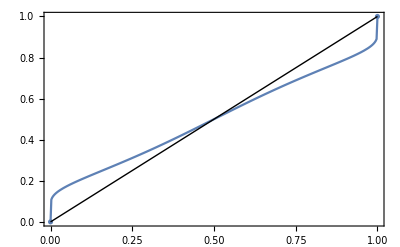

```mathematica
ProbabilityPlot[CauchyDistribution[0,1]]
```

```mathematica
PDF[CauchyDistribution[0,1],x]
```

1/(π (1+x^2))

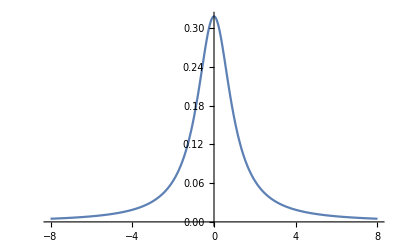

```mathematica
Plot[1/(π (1+x^2)),{x,-8,8}]
```

```mathematica
FindDistribution[Map[QuantityMagnitude@Last@#&,amzndiff2018]]
```

LaplaceDistribution[1.25409,23.5249]

```mathematica
PDF[LaplaceDistribution[1.254094645757424,23.52494001795228],x]
```

Piecewise[{{0.021254 ⅇ^(-0.0425081 (-1.25409+x)), x≥1.25409}, {0.021254 ⅇ^(-0.0425081 (1.25409-x)), True}}]

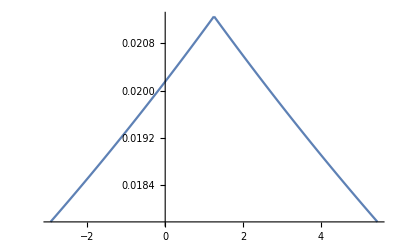

```mathematica
Plot[Piecewise[{{0.021254039313955385 ⅇ^(-0.04250807862791077 (-1.254094645757424+x)),x≥1.254094645757424}},0.021254039313955385 ⅇ^(-0.04250807862791077 (1.254094645757424-x))],{x,-2.9459053542425755,5.454094645757424}]
```

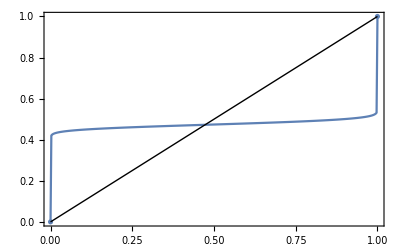

```mathematica
ProbabilityPlot[LaplaceDistribution[1.254094645757424,23.52494001795228]]
```

```mathematica
DateListPlot[Reverse@Map[Tooltip[#,{DateString@First@#,Last@#}]&,amzndiff2018],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
```

-Graphics-

```mathematica
FindDistributionParameters[Map[Last,amzndiff2018],LaplaceDistribution[μ,σ]]
```

{μ→2.84 $,σ→23.44 $}

```mathematica
FindDistribution[Map[QuantityMagnitude@Last@#&,amzndiff]]
```

CauchyDistribution[0.0121449,1.34716]

```mathematica
FindDistributionParameters[Map[Last,amzndiff2018],CauchyDistribution[μ,σ]]
```

{μ→4.30 $,σ→15.31 $}

```mathematica
FindDistributionParameters[Map[Last,amzndiff],CauchyDistribution[μ,σ]]
```

{μ→0.01 $,σ→1.35 $}

```mathematica
Grid@
{{"2018",All},
With[{amzndiff=amzndiff2018},{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}
]
,
{
With[{abs=Map[Abs@Last@#&,amzndiff]},
Grid@
Map[
{PercentForm@N@#,Quantile[abs,#]}&
,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}]
],
With[{diff=Map[Last,amzndiff],values=Map[Last,amzndiff[[;;10]]]},
With[{len=Length@diff},
Grid@
Map[Function[val,{val,PercentForm@N@((Length@Select[diff,val>#&])/len)}],values]
]]
}}
```

2018 | All
0% | 0.00 $
10% | 2.66 $
20% | 6.11 $
30% | 9.63 $
40% | 12.58 $
50% | 16.60 $
60% | 21.44 $
70% | 27.66 $
80% | 36.87 $
90% | 56.40 $
100% | 139.36 $ | 15.23 $ | 69.16%
11.19 $ | 63.49%
-22.42 $ | 18.14%
-0.26 $ | 42.63%
10.46 $ | 61.68%
-14.39 $ | 24.04%
-28.49 $ | 14.74%
26.72 $ | 83.9%
-43.69 $ | 8.163%
-8.86 $ | 31.07%
0% | 0.00 $
10% | 0.15 $
20% | 0.33 $
30% | 0.57 $
40% | 0.88 $
50% | 1.36 $
60% | 2.11 $
70% | 3.13 $
80% | 5.11 $
90% | 9.90 $
100% | 139.36 $ | 15.23 $ | 96.49%
11.19 $ | 94.98%
-22.42 $ | 1.863%
-0.26 $ | 40.23%
10.46 $ | 94.53%
-14.39 $ | 2.786%
-28.49 $ | 1.42%
26.72 $ | 98.53%
-43.69 $ | 0.6744%
-8.86 $ | 4.791%